Sorbonne Université  |               |                                     Atelier de Recherche Encadrée UE LU1SXARE ”Mesures”

__________________________________________________________________________

M 3 : Utilisation de Mathematica
__________________________________________________________________________

## Exercices

Le fichier doit être renommé exactement comme ceci :
	M3VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur MOODLE à la fin de la séance, et/ou avant la fin de la semaine de la séance.

# Ajustement : méthode des moindres carrés (Khi-Carré)

```mathematica
(* Enlève les cellules output*)
FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]
```

## I ) Ajustement de la loi d'absorption de photons dans la matière (loi de Beer - Lambert)

A) Visualisation de la d’absorption de photons dans la matière (loi de  Beer - Lambert) : n(x) =  A Exp[- mu x] .                                                                                                                                                                                    Vous prendrez A = 10 et mu = 0.5. Que représentent les paramètres A et mu ? Les nommer.

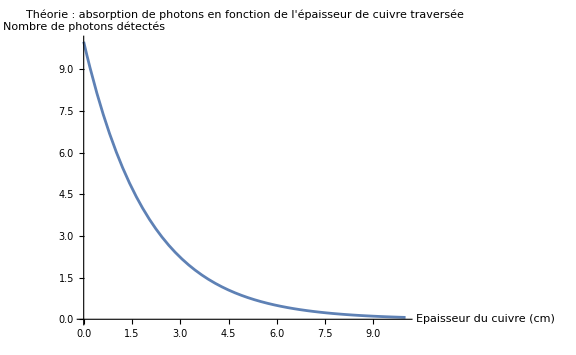

```mathematica
Plot[ 10 Exp[- 0.5 x],{x,0,10},AxesLabel->{"Epaisseur du cuivre (cm)","Nombre de photons détectés"},PlotLabel->"Théorie : absorption de photons en fonction de l'épaisseur de cuivre traversée", ImageSize->Large]
```

B ) Écrire l’équation différentielle qui régit le nombre de photons et la solutionner en utilisant Mathematica.

```mathematica
Clear[n,x]
nSol = DSolveValue[{n'[x] == - 0.5 n[x], n[0] == 10},n,x]
```

Function[{x},10. ⅇ^(-0.5 x)]

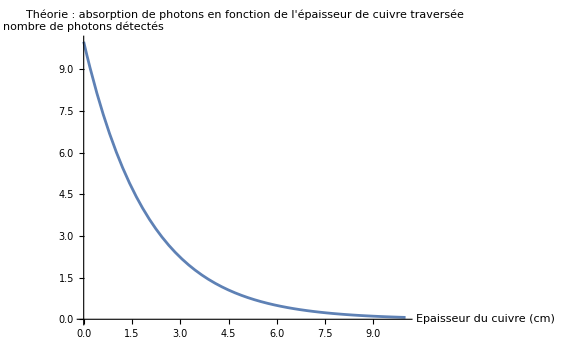

```mathematica
Plot[ nSol[x],{x,0,10},AxesLabel->{"Epaisseur du cuivre (cm)","nombre de photons détectés"},PlotLabel->"Théorie : absorption de photons en fonction de l'épaisseur de cuivre traversée", ImageSize->Large]
```

C) On a mesuré le nombre (n) de photons  et l’erreur de mesure (en)  en fonction de l’épaisseur en cm de cuivre traversée (x)  par les photons.                                                                                                     dataPhotons  =  {{0,Around[43902,123]},{1,Around[24042,138]},{2,Around[12254,139]},{3,Around[6650,119]}}. Donner la définition de la fonction Around[]

```mathematica
dataPhotons = {{0,Around[43902,1230]},{1,Around[24042,1380]},{2,Around[12254,1390]},{3,Around[6650,1190]}}
```

{{0,4.390.1210^4},{1,2.400.1410^4},{2,1.230.1410^4},{3,6.71.210^3}}

C1) Représenter graphiquement  la liste de mesures : dataPhotons

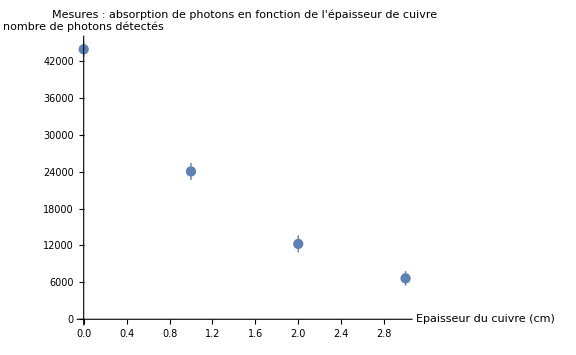

```mathematica
listPlotMesures = ListPlot[dataPhotons,AxesLabel->{"Epaisseur du cuivre (cm)","nombre de photons détectés"},PlotLabel->"Mesures : absorption de photons en fonction de l'épaisseur de cuivre",
ImageSize->Large]
```

C2) Comprendre les instructions ci-dessous qui donne une valeur approchée du paramètre A et mu, puis représente graphiquement la loi de Beer - Lambert ainsi trouvée en la superposant à la représentation graphique des mesures.

```mathematica
a0 = dataPhotons [[1]][[2]][[1]]
```

43902.

```mathematica
nP1 =  dataPhotons [[1]][[2]][[1]]
xP1 =  dataPhotons [[1]][[1]]
nP2 =  dataPhotons [[4]][[2]][[1]]
xP2=  dataPhotons [[4]][[1]]
mu0 = -(Log[nP2] - Log[nP1]) /(xP2-xP1)
```

43902.

0

6650.

3

0.629114

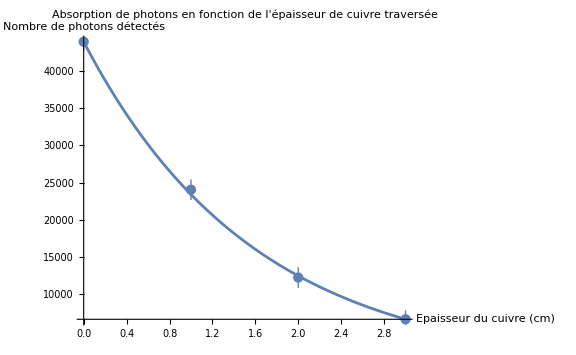

```mathematica
Show[Plot[ a0 * Exp[- mu0 *  x],{x,0,3}], listPlotMesures,AxesLabel->{"Epaisseur du cuivre (cm)","Nombre de photons détectés"},PlotLabel->"Absorption de photons en fonction de l'épaisseur de cuivre traversée", ImageSize->Large ]
```

D) Peut-on faire mieux ?  Pour répondre,  consulter  la partie modélisation des mesures par ajustement paramétrique en utilisant la méthode des moindres carrés du fichier  TP-Mesures-TH.pdf .  Réponse : Oui et  c’est ce que l’on va faire par la suite

E.1) Donner  la définition du résidu pondéré par l’erreur dans la théorie des moindres carrés.  A partir des mesures données par la table dataPhoton nous allons  fabriquer une table des résidus pondérés par les erreurs en suivant les étapes ci-dessous.  Bien comprendre les étapes.

E.1.2) Créer la table des épaisseurs de matière  traversées par les photons.

```mathematica
tabEpaisseur = Table[ dataPhotons [[i]][[1]], {i, 1, Length[dataPhotons]}]
```

{0,1,2,3}

E.1.3) Créer la table du nombre de photons  après les  épaisseurs de matière  traversées.

```mathematica
TabNbPhotons = Table[ dataPhotons [[i]][[2]][[1]], {i, 1, Length[dataPhotons]}]
```

{43902.,24042.,12254.,6650.}

E.1.4) Créer la table de l’erreur sur le nombre de photons  après les  épaisseurs de matière  traversées.

```mathematica
TabErreurPhotons = Table[ dataPhotons [[i]][[2]][[2]], {i, 1, Length[dataPhotons]}]
```

{1230.,1380.,1390.,1190.}

E.1.5) Créer la table du nombre de photons  après les  épaisseurs de matière  traversées si le nombre de photons suit la loi : n(x) =  A Exp[- mu x] .

```mathematica
n[x_] := a Exp[-mu x]
```

```mathematica
n[x]
```

a ⅇ^(-mu x)

```mathematica
TabNbPhotonsLoiBeerLambert = Map[n,tabEpaisseur]
```

{a,a ⅇ^-mu,a ⅇ^(-2 mu),a ⅇ^(-3 mu)}

```mathematica
{n[0],n[1],n[2],n[3]}
```

E.1.6) Créer la table des résidus.

```mathematica
tabResidus = Table[ TabNbPhotons[[i]] - TabNbPhotonsLoiBeerLambert[[i]] , {i, 1, Length[dataPhotons]}]
```

{43902.-a,24042.-a ⅇ^-mu,12254.-a ⅇ^(-2 mu),6650.-a ⅇ^(-3 mu)}

E.1.7) Créer la table des résidus pondérés par les erreurs?

```mathematica
tabResidusPonderes = Table[ (TabNbPhotons[[i]] - TabNbPhotonsLoiBeerLambert[[i]]) / TabErreurPhotons[[i]]  , {i, 1, Length[dataPhotons]}]
```

{0.000813008 (43902.-a),0.000724638 (24042.-a ⅇ^-mu),0.000719424 (12254.-a ⅇ^(-2 mu)),0.000840336 (6650.-a ⅇ^(-3 mu))}

F.1) Définir la  quantité appelée khi carré ou khi-deux, considéré comme une mesure du carré de la distance entre les données expérimentales et le modèle théorique qui prédit ces données qui prends en compte les erreurs de mesures.   Comme c’est généralement le cas, on dispose d’une estimation de  l’erreur qui affecte chaque mesure et  on l’utilise pour « pondérer » la contribution de la mesure au χ2.  Une mesure aura d’autant plus de poids que son incertitude sera faible. On notera cette fonction khiCarre(A,mu)

```mathematica
khiCarre[va_,vmu_] :=  Total[ tabResidusPonderes^2]/.{ a->va, mu->vmu}
```

```mathematica
khiCarre[n0,mu]
```

6.60982×10^-7 (43902.-n0)^2+7.06165×10^-7 (6650.-ⅇ^(-3 mu) n0)^2+5.17572×10^-7 (12254.-ⅇ^(-2 mu) n0)^2+5.251×10^-7 (24042.-ⅇ^-mu n0)^2

G.1) On veut déterminer la valeur des paramètres A et mu qui minimise la fonction khiCarre. Pour cela utiliser la fonction FindMinimum[]. Commentaire ?

```mathematica
khiCarreMinSol = FindMinimum[khiCarre[a,mu],{{a,40000},{mu, 0.6}}]
```

{0.203487,{a→44013.3,mu→0.6251}}

H .1) Commenter les instructions ci - dessous

{44013.3,0.6251}

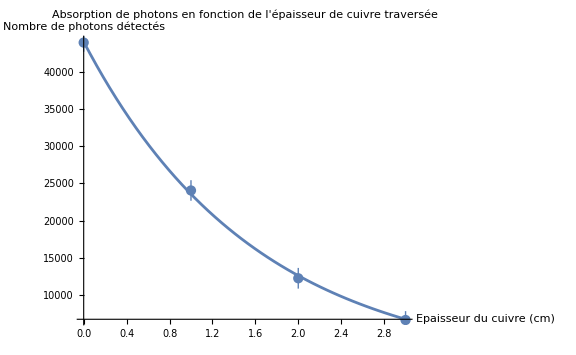

```mathematica
{a, mu} /. khiCarreMinSol[[2]]
Show[Plot[  a *Exp[- mu * x] /. khiCarreMinSol[[2]] ,{x,0,3}], listPlotMesures , AxesLabel->{"Epaisseur du cuivre (cm)","Nombre de photons détectés"},PlotLabel->"Absorption de photons en fonction de l'épaisseur de cuivre traversée", ImageSize->Large]
```

I)  Retrouver les valeurs des paramètres A et mu, qui minimise khiCarre(A,mu) la somme des moindres carrés pondérés par les erreurs de mesure en utilisant  NonlinearModelFit[] : Pour cela  :

I.1) Décrire brièvement la fonction  NonlinearModelFit[].

```mathematica
?NonlinearModelFit
```

I.2) Créer la liste de mesures  (dataPhotonsXY) de la forme { {x1,  n1}, {x2, n2}, ......}

```mathematica
dataPhotonsXY =  Table[ {tabEpaisseur[[i]],TabNbPhotons [[i]]}, {i, 1, Length[dataPhotons]}]
```

{{0,43902.},{1,24042.},{2,12254.},{3,6650.}}

I.3) Réaliser l’ajustement en utilisant la fonction  NonlinearModelFit[] , la liste dataPhotonsXY et le modèle d’ajustement  comme variables d’entrées.

```mathematica
nlmKhiCarre=NonlinearModelFit[dataPhotonsXY,A * Exp[- mu *x ],{A,mu},x, Weights->1/TabErreurPhotons^2]
```

FittedModel[…]

```mathematica
Normal[nlmKhiCarre]
```

44013.3 ⅇ^(-0.6251 x)

```mathematica
nlmKhiCarre[0]
```

44013.3

```mathematica
{nlmKhiCarre["ParameterTable"]}
```

{ | Estimate | Standard Error | t-Statistic | P-Value
A | 44013.3 | 381.97 | 115.227 | 0.0000753082
mu | 0.6251 | 0.0118148 | 52.9081 | 0.000357046}

```mathematica
Show[Plot[ nlmKhiCarre[ x],{x,0,3}], listPlotMesures , AxesLabel->{"Epaisseur du cuivre (cm)","Nombre de photons détectés"},PlotLabel->"Absorption de photons en fonction de l'épaisseur de cuivre traversée", ImageSize->Large]
```

-Graphics-

```mathematica
Problème A : Refaire l'étude avec les mesures suivantes :  {{0, Around[83704, 2890]}, {1, Around[61683, 2480]}, {2, Around[53273, 2300]}, {4, Around[30600, 1750]}}. Donner la loi de Beer - Lambert correspondante.
```

```mathematica
dataPhotons1 = {{0, Around[83704, 2890]}, {1, Around[61683, 2480]}, {2, Around[53273, 2300]}, {4, Around[30600, 1750]}}
TabErreurPhotons1 = Table[ dataPhotons [[i]][[2]][[2]], {i, 1, Length[dataPhotons]}]



(*tabEpaisseur1 = Table[ dataPhotons1 [[i]][[1]], {i, 1, Length[dataPhotons1]}]
TabNbPhotonsLoiBeerLambert1 = Map[n,tabEpaisseur1]

TabNbPhotons1 = Table[ dataPhotons [[i]][[2]][[1]], {i, 1, Length[dataPhotons]}]
tabResidusPonderes1 = Table[ (TabNbPhotons1[[i]] - TabNbPhotonsLoiBeerLambert1[[i]]) / TabErreurPhotons1[[i]]  , {i, 1, Length[dataPhotons1]}]*)
```

{{0,8.370.2910^4},{1,6.170.2510^4},{2,5.330.2310^4},{4,3.060.1810^4}}

# Contrôle continu : CC3

## Refaire l'analyse des mesures de la section I.5 en utilisant la liste de mesure ci-dessous qui décrit le nombre de photons détectés en fonction de la distance à la source. Vous ajusterez la fonction x --> a/(b + x)^2 .Commentaire? {{10,Around[276593,4176]},{20,Around[82926,2496]},{30,Around[35301,2576]},{40,Around[20098,2248]},{50,Around[14335,1708]},{60,Around [10990,953]},{70,Around[7990,997]}}